```mathematica
Clear["Global`*"]
```

```mathematica
(*E0,Vb,α,γ0,ϕV1p*)
```

```mathematica
E0=1.0;Vb=2.0;α=0.0Degree;γ0=1.0;ϕV1p=0.0Degree
```

0.

### angles

```mathematica
ϕV1[ϕV1p_,α_]:=ϕV1p+α
```

```mathematica
ϕV1[ϕV1p,α]
```

0.

```mathematica
ϕk1[ϕV1p_,α_,γ0_]:=ArcTan[1/γ0^2 Tan[ϕV1[ϕV1p,α]]]
```

```mathematica
ϕk1[ϕV1p,α,γ0]
```

0.

```mathematica
ϕs1[ϕV1p_,α_,γ0_]:=ArcTan[1/γ0 Tan[ϕV1[ϕV1p,α]]]
```

```mathematica
ϕs1[ϕV1p,α,γ0]
```

0.

```mathematica
ϕk1p[ϕV1p_,α_,γ0_] := ϕk1[ϕV1p,α,γ0]-α
```

```mathematica
ϕk1p[ϕV1p,α,γ0]
```

0.

```mathematica
ϕs1p[ϕV1p_,α_,γ0_] := ϕs1[ϕV1p,α,γ0]-α
```

```mathematica
ϕs1p[ϕV1p,α,γ0]
```

0.

```mathematica
{ϕV1p,ϕs1p[ϕV1p,α,γ0],ϕk1p[ϕV1p,α,γ0]}
```

{0.,0.,0.}

```mathematica
{ϕV1[ϕV1p,α],ϕs1[ϕV1p,α,γ0],ϕk1[ϕV1p,α,γ0]}
```

{0.,0.,0.}

### k-vector before the barrier - {k1x, k1y} --> {k1xp, k1yp}

```mathematica
k1[ϕV1p_,α_,γ0_,En_]:=Module[
{t1,k1},
t1=Cos[ϕk1[ϕV1p,α,γ0]]^2+γ0^2 Sin[ϕk1[ϕV1p,α,γ0]]^2;
k1=En/(√t1);
{1.k1 Cos[ϕk1[ϕV1p,α,γ0]],1.k1 Sin[ϕk1[ϕV1p,α,γ0]]}
]
```

```mathematica
k1[1.0,α,γ0,E0]
```

{0.540302,0.841471}

```mathematica
RotM[α_]:={
{Cos[α],-Sin[α]},
{Sin[α],Cos[α]}
}
```

```mathematica
(*k1p[ϕV1p_,α_,γ0_,En_]:=Module[
{t1,k1},
t1=Cos[ϕk1[ϕV1p,α,γ0]]^2+γ0^2 Sin[ϕk1[ϕV1p,α,γ0]]^2;
k1=En/(√t1);
{1.k1 Cos[ϕk1p[ϕV1p,α,γ0]],1.k1 Sin[ϕk1p[ϕV1p,α,γ0]]}
]*)
```

```mathematica
(*k1p[ϕV1p,α,γ0,E0]*)
```

```mathematica
k1p[ϕV1p_,α_,γ0_,En_]:=RotM[-α].k1[ϕV1p,α,γ0,En]
```

```mathematica
k1yp[ϕV1p_,α_,γ0_,En_]:=k1p[ϕV1p,α,γ0,En][[2]]
```

```mathematica
k1p[ϕV1p,α,γ0,E0]
```

{1.,0.}

```mathematica
k1yp[ϕV1p,α,γ0,E0]
```

0.

### (*kyP*)

```mathematica
KyP=k1yp[ϕV1p,α,γ0,E0]
```

0.

```mathematica
RotM[α].k1p[ϕV1p,α,γ0,E0] (* = k1 *)
```

{1.,0.}

```mathematica
(*E0,Vb,α,γ0,ϕV1p*)
```

```mathematica
TwoKxPs[ϕV1p_,α_,γ0_,En_]:=Module[
{
Eq11,Eq12,Eq13,
Sol,Sol1,Sol2,
KyP,
kxpI1,kxpI2
},
KyP=k1yp[ϕV1p,α,γ0,En];
Eq11=(RotM[α].{k1xp,KyP})[[1]]=={k1x,k1y}[[1]];
Eq12=(RotM[α].{k1xp,KyP})[[2]]=={k1x,k1y}[[2]];
Eq13=k1x^2+(γ0 k1y)^2==En^2;
Sol=NSolve[
{Eq11,Eq12,Eq13},
{k1x,k1y,k1xp}
];
Sol1=Sol[[1]];
Sol2=Sol[[2]];
{k1xp/.Sol1,k1xp/.Sol2}
]
```

```mathematica
TwoKxPs[ϕV1p,α,γ0,E0]
```

{-1.,1.}

```mathematica
Wave1P[ϕV1p_,α_,γ0_,En_]:={
TwoKxPs[ϕV1p,α,γ0,En][[1]],k1yp[ϕV1p,α,γ0,En]}
```

```mathematica
Wave1P[ϕV1p,α,γ0,E0]
```

{-1.,0.}

```mathematica
Wave1[ϕV1p_,α_,γ0_,En_]:=RotM[α].Wave1P[ϕV1p,α,γ0,En]
```

```mathematica
Wave1[ϕV1p,α,γ0,E0]
```

{-1.,0.}

```mathematica
Wave2P[ϕV1p_,α_,γ0_,En_]:={
TwoKxPs[ϕV1p,α,γ0,En][[2]],k1yp[ϕV1p,α,γ0,En]}
```

```mathematica
Wave2P[ϕV1p,α,γ0,E0]
```

{1.,0.}

```mathematica
Wave2[ϕV1p_,α_,γ0_,En_]:=RotM[α].Wave2P[ϕV1p,α,γ0,En]
```

```mathematica
Wave2[ϕV1p,α,γ0,E0]
```

{1.,0.}

```mathematica
VWave1[ϕV1p_,α_,γ0_,En_]:={Wave1[ϕV1p,α,γ0,En][[1]],γ0^2 Wave1[ϕV1p,α,γ0,En][[2]]}
```

```mathematica
VWave2[ϕV1p_,α_,γ0_,En_]:={Wave2[ϕV1p,α,γ0,En][[1]],γ0^2 Wave2[ϕV1p,α,γ0,En][[2]]}
```

```mathematica
VWave1P[ϕV1p_,α_,γ0_,En_]:=RotM[-α].VWave1[ϕV1p,α,γ0,En]
```

```mathematica
VWave2P[ϕV1p_,α_,γ0_,En_]:=RotM[-α].VWave2[ϕV1p,α,γ0,En]
```

```mathematica
VWave1P[ϕV1p,α,γ0,E0]
```

{-1.,0.}

```mathematica
VWave2P[ϕV1p,α,γ0,E0]
```

{1.,0.}

```mathematica
RefWaveP[ϕV1p_,α_,γ0_,En_]:=If[
VWave1P[ϕV1p,α,γ0,En][[1]]<0,
Wave1P[ϕV1p,α,γ0,En],
Wave2P[ϕV1p,α,γ0,En]
]
```

```mathematica
RefWaveP[ϕV1p,α,γ0,E0]
```

{-1.,0.}

```mathematica
RefWave[ϕV1p_,α_,γ0_,En_]:=RotM[α].RefWaveP[ϕV1p,α,γ0,En]
```

```mathematica
RefWave[ϕV1p,α,γ0,E0]
```

{-1.,0.}

```mathematica
TransWaveP[ϕV1p_,α_,γ0_,En_]:=If[
VWave1P[ϕV1p,α,γ0,En][[1]]>0,
Wave1P[ϕV1p,α,γ0,En],
Wave2P[ϕV1p,α,γ0,En]
]
```

```mathematica
TransWaveP[ϕV1p,α,γ0,E0]
```

{1.,0.}

```mathematica
TransWave[ϕV1p_,α_,γ0_,En_]:=RotM[α].TransWaveP[ϕV1p,α,γ0,En]
```

```mathematica
TransWave[ϕV1p,α,γ0,E0]
```

{1.,0.}

```mathematica
(* k1xp - 7th (last) unknown *)
```

```mathematica
k1xp[ϕV1p_,α_,γ0_,En_]:=TransWaveP[ϕV1p,α,γ0,En][[1]]
```

```mathematica
k1xp[ϕV1p,α,γ0,E0]
```

1.

```mathematica
Wave2[ϕV1p,α,γ0,E0]
```

{1.,0.}

```mathematica
√((RefWave[ϕV1p,α,γ0,E0][[1]])^2+(γ0 RefWave[ϕV1p,α,γ0,E0][[2]])^2)
```

1.

```mathematica
√((TransWave[ϕV1p,α,γ0,E0][[1]])^2+(γ0 TransWave[ϕV1p,α,γ0,E0][[2]])^2)
```

1.

```mathematica
√((Wave1[ϕV1p,α,γ0,E0][[1]])^2+(γ0 Wave1[ϕV1p,α,γ0,E0][[2]])^2)
```

1.

```mathematica
√((Wave2[ϕV1p,α,γ0,E0][[1]])^2+(γ0 Wave2[ϕV1p,α,γ0,E0][[2]])^2)
```

1.

```mathematica
VRefWaveP[ϕV1p_,α_,γ0_,En_]:=RotM[-α].{RefWave[ϕV1p,α,γ0,En][[1]],γ0^2 RefWave[ϕV1p,α,γ0,En][[2]]}
```

```mathematica
VTransWaveP[ϕV1p_,α_,γ0_,En_]:=RotM[-α].{TransWave[ϕV1p,α,γ0,En][[1]],γ0^2 TransWave[ϕV1p,α,γ0,En][[2]]}
```

### Angles for reflected wave

```mathematica
Angleϕ[kx_,ky_]:=Module[
{t1},
t1=ArcTan[ky/kx];
If[kx>0,t1,t1-Abs@π]
]
```

```mathematica
Angleϕ[-1,-√3]
```

-(2 π)/3

```mathematica
{ϕV1p,ϕs1p[ϕV1p,α,γ0],ϕk1p[ϕV1p,α,γ0]}
```

{0.,0.,0.}

```mathematica
{ϕV1[ϕV1p,α],ϕs1[ϕV1p,α,γ0],ϕk1[ϕV1p,α,γ0]}
```

{0.,0.,0.}

```mathematica
Oϕk[ϕV1p_,α_,γ0_,En_]:=Angleϕ[TransWave[ϕV1p,α,γ0,En][[1]],TransWave[ϕV1p,α,γ0,En][[2]]]
```

```mathematica
Oϕk[ϕV1p,α,γ0,E0]
```

0.

```mathematica
(* Oϕs ϕs1 - 1st unknown *)
```

```mathematica
Oϕs[ϕV1p_,α_,γ0_,En_]:=Angleϕ[TransWave[ϕV1p,α,γ0,En][[1]],γ0 TransWave[ϕV1p,α,γ0,En][[2]]]
```

```mathematica
Oϕs[ϕV1p,α,γ0,E0]
```

0.

```mathematica
OϕV[ϕV1p_,α_,γ0_,En_]:=Angleϕ[TransWave[ϕV1p,α,γ0,En][[1]],γ0^2 TransWave[ϕV1p,α,γ0,En][[2]]]
```

```mathematica
OϕV[ϕV1p,α,γ0,E0]
```

0.

```mathematica
Oϕkr[ϕV1p_,α_,γ0_,En_]:=Angleϕ[RefWave[ϕV1p,α,γ0,En][[1]],RefWave[ϕV1p,α,γ0,En][[2]]]
```

```mathematica
Oϕkr[ϕV1p,α,γ0,E0]
```

-3.14159

```mathematica
(* Oϕsr ϕs1r - 2st unknown *)
```

```mathematica
Oϕsr[ϕV1p_,α_,γ0_,En_]:=Angleϕ[RefWave[ϕV1p,α,γ0,En][[1]],γ0 RefWave[ϕV1p,α,γ0,En][[2]]]
```

```mathematica
Oϕsr[ϕV1p,α,γ0,E0]
```

-3.14159

## k-vector at the barrier region - {k2x, k2y} --> {k2xp, k2yp}

```mathematica
(*KyP=0.0(*k1yp[ϕV1p,α,γ0,E0]*)
```

```mathematica
(*E0,Vb,α,γ0,ϕV1p*)
```

```mathematica
TwoKxPs2[ϕV1p_,α_,γ0_,En_,Vb_]:=Module[
{
Eq11,Eq12,Eq13,
Sol,Sol1,Sol2,
KyP,
kxpI1,kxpI2
},
KyP=k1yp[ϕV1p,α,γ0,En];
Eq11=(RotM[α].{k1xp,KyP})[[1]]=={k1x,k1y}[[1]];
Eq12=(RotM[α].{k1xp,KyP})[[2]]=={k1x,k1y}[[2]];
Eq13=k1x^2+(γ0 k1y)^2==(En-Vb)^2;
Sol=NSolve[
{Eq11,Eq12,Eq13},
{k1x,k1y,k1xp}
];
Sol1=Sol[[1]];
Sol2=Sol[[2]];
{k1xp/.Sol1,k1xp/.Sol2}
]
```

```mathematica
TwoKxPs2[ϕV1p,α,γ0,E0,Vb]
```

{-1.,1.}

```mathematica
Wave1P2[ϕV1p_,α_,γ0_,En_,Vb_]:={
TwoKxPs2[ϕV1p,α,γ0,En,Vb][[1]],k1yp[ϕV1p,α,γ0,En]}
```

```mathematica
Wave1P2[ϕV1p,α,γ0,E0,Vb]
```

{-1.,0.}

```mathematica
Wave12[ϕV1p_,α_,γ0_,En_,Vb_]:=RotM[α].Wave1P2[ϕV1p,α,γ0,En,Vb]
```

```mathematica
Wave12[ϕV1p,α,γ0,E0,Vb]
```

{-1.,0.}

```mathematica
Wave2P2[ϕV1p_,α_,γ0_,En_,Vb_]:={
TwoKxPs2[ϕV1p,α,γ0,En,Vb][[2]],k1yp[ϕV1p,α,γ0,En]}
```

```mathematica
Wave2P2[ϕV1p,α,γ0,E0,Vb]
```

{1.,0.}

```mathematica
Wave22[ϕV1p_,α_,γ0_,En_,Vb_]:=RotM[α].Wave2P2[ϕV1p,α,γ0,En,Vb]
```

```mathematica
Wave22[ϕV1p,α,γ0,E0,Vb]
```

{1.,0.}

```mathematica
VWave12[ϕV1p_,α_,γ0_,En_,Vb_]:={Wave12[ϕV1p,α,γ0,En,Vb][[1]],γ0^2 Wave12[ϕV1p,α,γ0,En,Vb][[2]]}
```

```mathematica
VWave22[ϕV1p_,α_,γ0_,En_,Vb_]:={Wave22[ϕV1p,α,γ0,En,Vb][[1]],γ0^2 Wave22[ϕV1p,α,γ0,En,Vb][[2]]}
```

```mathematica
VWave12P[ϕV1p_,α_,γ0_,En_,Vb_]:=RotM[-α].VWave12[ϕV1p,α,γ0,En,Vb]
```

```mathematica
VWave22P[ϕV1p_,α_,γ0_,En_,Vb_]:=RotM[-α].VWave22[ϕV1p,α,γ0,En,Vb]
```

```mathematica
VWave12P[ϕV1p,α,γ0,E0,Vb]
```

{-1.,0.}

```mathematica
VWave22P[ϕV1p,α,γ0,E0,Vb]
```

{1.,0.}

```mathematica
RefWave2P[ϕV1p_,α_,γ0_,En_,Vb_]:=If[
VWave12P[ϕV1p,α,γ0,En,Vb][[1]]<0,
Wave1P2[ϕV1p,α,γ0,En,Vb],
Wave2P2[ϕV1p,α,γ0,En,Vb]
]
```

```mathematica
RefWave2P[ϕV1p,α,γ0,E0,Vb]
```

{-1.,0.}

```mathematica
(* k2xpR - 6th unknown *)
```

```mathematica
k2xpR[ϕV1p_,α_,γ0_,En_,Vb_]:=RefWave2P[ϕV1p,α,γ0,En,Vb][[1]]
```

```mathematica
k2xpR[ϕV1p,α,γ0,E0,Vb]
```

-1.

```mathematica
RefWave2[ϕV1p_,α_,γ0_,En_,Vb_]:=RotM[α].RefWave2P[ϕV1p,α,γ0,En,Vb]
```

```mathematica
RefWave2[ϕV1p,α,γ0,E0,Vb]
```

{-1.,0.}

```mathematica
TransWave2P[ϕV1p_,α_,γ0_,En_,Vb_]:=If[
VWave12P[ϕV1p,α,γ0,En,Vb][[1]]>0,
Wave1P2[ϕV1p,α,γ0,En,Vb],
Wave2P2[ϕV1p,α,γ0,En,Vb]
]
```

```mathematica
TransWave2P[ϕV1p,α,γ0,E0,Vb]
```

{1.,0.}

```mathematica
TransWave2[ϕV1p_,α_,γ0_,En_,Vb_]:=RotM[α].TransWave2P[ϕV1p,α,γ0,En,Vb]
```

```mathematica
TransWave2[ϕV1p,α,γ0,E0,Vb]
```

{1.,0.}

```mathematica
(* k2xp - 5th unknown *)
```

```mathematica
k2xp[ϕV1p_,α_,γ0_,En_,Vb_]:=TransWave2P[ϕV1p,α,γ0,En,Vb][[1]]
```

```mathematica
k2xp[ϕV1p,α,γ0,E0,Vb]
```

1.

```mathematica
Wave1P2[ϕV1p,α,γ0,E0,Vb]
```

{-1.,0.}

```mathematica
Wave2P2[ϕV1p,α,γ0,E0,Vb]
```

{1.,0.}

```mathematica
√((RefWave2[ϕV1p,α,γ0,E0,Vb][[1]])^2+(γ0 RefWave2[ϕV1p,α,γ0,E0,Vb][[2]])^2)
```

1.

```mathematica
√((TransWave2[ϕV1p,α,γ0,E0,Vb][[1]])^2+(γ0 TransWave2[ϕV1p,α,γ0,E0,Vb][[2]])^2)
```

1.

```mathematica
√((Wave12[ϕV1p,α,γ0,E0,Vb][[1]])^2+(γ0 Wave12[ϕV1p,α,γ0,E0,Vb][[2]])^2)
```

1.

```mathematica
√((Wave22[ϕV1p,α,γ0,E0,Vb][[1]])^2+(γ0 Wave22[ϕV1p,α,γ0,E0,Vb][[2]])^2)
```

1.

### Angles for reflected wave

```mathematica
Angleϕ[kx_,ky_]:=Module[
{t1},
t1=ArcTan[ky/kx];
If[kx>0,t1,t1+π]
]
```

```mathematica
Angleϕ[-1,-√3]
```

(4 π)/3

```mathematica
Oϕk2[ϕV1p_,α_,γ0_,En_,Vb_]:=Angleϕ[TransWave2[ϕV1p,α,γ0,En,Vb][[1]],TransWave2[ϕV1p,α,γ0,En,Vb][[2]]]
```

```mathematica
Oϕk2[ϕV1p,α,γ0,E0,Vb]
```

0.

```mathematica
(* Oϕs ϕs2 - 3rd unknown *)
```

```mathematica
Oϕs2[ϕV1p_,α_,γ0_,En_,Vb_]:=Angleϕ[TransWave2[ϕV1p,α,γ0,En,Vb][[1]],γ0 TransWave2[ϕV1p,α,γ0,En,Vb][[2]]]
```

```mathematica
Oϕs2[ϕV1p,α,γ0,E0,Vb]
```

0.

```mathematica
OϕV2[ϕV1p_,α_,γ0_,En_,Vb_]:=Angleϕ[TransWave2[ϕV1p,α,γ0,En,Vb][[1]],γ0^2 TransWave2[ϕV1p,α,γ0,En,Vb][[2]]]
```

```mathematica
OϕV2[ϕV1p,α,γ0,E0,Vb]
```

0.

```mathematica
Oϕkr2[ϕV1p_,α_,γ0_,En_,Vb_]:=Angleϕ[RefWave2[ϕV1p,α,γ0,En,Vb][[1]],RefWave2[ϕV1p,α,γ0,En,Vb][[2]]]
```

```mathematica
Oϕkr2[ϕV1p,α,γ0,E0,Vb]
```

3.14159

```mathematica
(* Oϕsr ϕs2r - 4th unknown *)
```

```mathematica
Oϕsr2[ϕV1p_,α_,γ0_,En_,Vb_]:=Angleϕ[RefWave2[ϕV1p,α,γ0,En,Vb][[1]],γ0 RefWave2[ϕV1p,α,γ0,En,Vb][[2]]]
```

```mathematica
Oϕsr2[ϕV1p,α,γ0,E0,Vb]
```

3.14159

## Calculation of the transmission

```mathematica
Clear[Eq1,Eq2,Eq3,Eq4,t,TSol]
```

```mathematica
Eq1:=1+r==s(a+b)
```

```mathematica
Eq2:=Cos[ϕs1]+r Cos[ϕs1r]==a Cos[ϕs2]+b Cos[ϕs2r]
```

```mathematica
Eq3:=a Exp[ⅈ k2xp Wb]+b Exp[ⅈ k2xpR Wb]==t s Exp[ⅈ k1xp Wb]
```

```mathematica
Eq4:=a Cos[ϕs2]Exp[ⅈ k2xp Wb]+b Cos[ϕs2r]Exp[ⅈ k2xpR Wb]==t Cos[ϕs1]Exp[ⅈ k1xp Wb]
```

```mathematica
ts=(t/.Solve[
{Eq1,Eq2,Eq3,Eq4},
{r,a,b,t}
]/.{s^2->1,s^4->1})[[1]]
```

(ⅇ^(-ⅈ k1xp Wb+ⅈ k2xp Wb+ⅈ k2xpR Wb) (Cos[ϕs1]-Cos[ϕs1r]) (Cos[ϕs2]-Cos[ϕs2r]))/(ⅇ^(ⅈ k2xp Wb) s Cos[ϕs1] Cos[ϕs1r]-ⅇ^(ⅈ k2xpR Wb) s Cos[ϕs1] Cos[ϕs1r]+ⅇ^(ⅈ k2xpR Wb) Cos[ϕs1] Cos[ϕs2]-ⅇ^(ⅈ k2xp Wb) Cos[ϕs1r] Cos[ϕs2]-ⅇ^(ⅈ k2xp Wb) Cos[ϕs1] Cos[ϕs2r]+ⅇ^(ⅈ k2xpR Wb) Cos[ϕs1r] Cos[ϕs2r]+ⅇ^(ⅈ k2xp Wb) s Cos[ϕs2] Cos[ϕs2r]-ⅇ^(ⅈ k2xpR Wb) s Cos[ϕs2] Cos[ϕs2r])

```mathematica
t[ϕs1_,ϕs1r_,ϕs2_,ϕs2r_,k2xp_,k2xpR_,k1xp_,Wb_,s_]:=(ⅇ^(-ⅈ k1xp Wb+ⅈ k2xp Wb+ⅈ k2xpR Wb) (Cos[ϕs1]-Cos[ϕs1r]) (Cos[ϕs2]-Cos[ϕs2r]))/(ⅇ^(ⅈ k2xp Wb) s Cos[ϕs1] Cos[ϕs1r]-ⅇ^(ⅈ k2xpR Wb) s Cos[ϕs1] Cos[ϕs1r]+ⅇ^(ⅈ k2xpR Wb) Cos[ϕs1] Cos[ϕs2]-ⅇ^(ⅈ k2xp Wb) Cos[ϕs1r] Cos[ϕs2]-ⅇ^(ⅈ k2xp Wb) Cos[ϕs1] Cos[ϕs2r]+ⅇ^(ⅈ k2xpR Wb) Cos[ϕs1r] Cos[ϕs2r]+ⅇ^(ⅈ k2xp Wb) s Cos[ϕs2] Cos[ϕs2r]-ⅇ^(ⅈ k2xpR Wb) s Cos[ϕs2] Cos[ϕs2r])
```

```mathematica
TSol[V0_,E0_,ϕV1p_,Wb_,α_,γ0_]:=Module[
{
Iϕs1,Iϕs1r,
Iϕs2,Iϕs2r,
Ik2xp,Ik2xpR,
Ik1xp,
s
},
Iϕs1=Oϕs[ϕV1p,α,γ0,E0];
Iϕs1r=Oϕsr[ϕV1p,α,γ0,E0];
Iϕs2=Oϕs2[ϕV1p,α,γ0,E0,V0];
Ik1xp=k1xp[ϕV1p,α,γ0,E0];
Iϕs2r=Oϕsr2[ϕV1p,α,γ0,E0,V0];
Ik2xp=k2xp[ϕV1p,α,γ0,E0,V0];
Ik2xpR=k2xpR[ϕV1p,α,γ0,E0,V0];
(**)
s=Sign[E0]Sign[E0-V0];
(Abs@t[Iϕs1,Iϕs1r,Iϕs2,Iϕs2r,Ik2xp,Ik2xpR,Ik1xp,Wb,s])^2
]
```

```mathematica
TSol[15.0,1.0,0,2.0,0.0,1.0]
```

1.

```mathematica
rs=(r/.Solve[
{Eq1,Eq2,Eq3,Eq4},
{r,a,b,t}
]/.{s^2->1,s^4->1})[[1]]
```

-((-ⅇ^(ⅈ k2xp Wb) s Cos[ϕs1]^2+ⅇ^(ⅈ k2xpR Wb) s Cos[ϕs1]^2+ⅇ^(ⅈ k2xp Wb) Cos[ϕs1] Cos[ϕs2]-ⅇ^(ⅈ k2xpR Wb) Cos[ϕs1] Cos[ϕs2]+ⅇ^(ⅈ k2xp Wb) Cos[ϕs1] Cos[ϕs2r]-ⅇ^(ⅈ k2xpR Wb) Cos[ϕs1] Cos[ϕs2r]-ⅇ^(ⅈ k2xp Wb) s Cos[ϕs2] Cos[ϕs2r]+ⅇ^(ⅈ k2xpR Wb) s Cos[ϕs2] Cos[ϕs2r])/(-ⅇ^(ⅈ k2xp Wb) s Cos[ϕs1] Cos[ϕs1r]+ⅇ^(ⅈ k2xpR Wb) s Cos[ϕs1] Cos[ϕs1r]-ⅇ^(ⅈ k2xpR Wb) Cos[ϕs1] Cos[ϕs2]+ⅇ^(ⅈ k2xp Wb) Cos[ϕs1r] Cos[ϕs2]+ⅇ^(ⅈ k2xp Wb) Cos[ϕs1] Cos[ϕs2r]-ⅇ^(ⅈ k2xpR Wb) Cos[ϕs1r] Cos[ϕs2r]-ⅇ^(ⅈ k2xp Wb) s Cos[ϕs2] Cos[ϕs2r]+ⅇ^(ⅈ k2xpR Wb) s Cos[ϕs2] Cos[ϕs2r]))

```mathematica
r[ϕs1_,ϕs1r_,ϕs2_,ϕs2r_,k2xp_,k2xpR_,k1xp_,Wb_,s_]:=-((-ⅇ^(ⅈ k2xp Wb) s Cos[ϕs1]^2+ⅇ^(ⅈ k2xpR Wb) s Cos[ϕs1]^2+ⅇ^(ⅈ k2xp Wb) Cos[ϕs1] Cos[ϕs2]-ⅇ^(ⅈ k2xpR Wb) Cos[ϕs1] Cos[ϕs2]+ⅇ^(ⅈ k2xp Wb) Cos[ϕs1] Cos[ϕs2r]-ⅇ^(ⅈ k2xpR Wb) Cos[ϕs1] Cos[ϕs2r]-ⅇ^(ⅈ k2xp Wb) s Cos[ϕs2] Cos[ϕs2r]+ⅇ^(ⅈ k2xpR Wb) s Cos[ϕs2] Cos[ϕs2r])/(-ⅇ^(ⅈ k2xp Wb) s Cos[ϕs1] Cos[ϕs1r]+ⅇ^(ⅈ k2xpR Wb) s Cos[ϕs1] Cos[ϕs1r]-ⅇ^(ⅈ k2xpR Wb) Cos[ϕs1] Cos[ϕs2]+ⅇ^(ⅈ k2xp Wb) Cos[ϕs1r] Cos[ϕs2]+ⅇ^(ⅈ k2xp Wb) Cos[ϕs1] Cos[ϕs2r]-ⅇ^(ⅈ k2xpR Wb) Cos[ϕs1r] Cos[ϕs2r]-ⅇ^(ⅈ k2xp Wb) s Cos[ϕs2] Cos[ϕs2r]+ⅇ^(ⅈ k2xpR Wb) s Cos[ϕs2] Cos[ϕs2r]))
```

```mathematica
RSol[V0_,E0_,ϕV1p_,Wb_,α_,γ0_]:=Module[
{
Iϕs1,Iϕs1r,
Iϕs2,Iϕs2r,
Ik2xp,Ik2xpR,
Ik1xp,
s
},
Iϕs1=Oϕs[ϕV1p,α,γ0,E0];
Iϕs1r=Oϕsr[ϕV1p,α,γ0,E0];
Iϕs2=Oϕs2[ϕV1p,α,γ0,E0,V0];
Ik1xp=k1xp[ϕV1p,α,γ0,E0];
Iϕs2r=Oϕsr2[ϕV1p,α,γ0,E0,V0];
Ik2xp=k2xp[ϕV1p,α,γ0,E0,V0];
Ik2xpR=k2xpR[ϕV1p,α,γ0,E0,V0];
(**)
s=Sign[E0]Sign[E0-V0];
(Abs@r[Iϕs1,Iϕs1r,Iϕs2,Iϕs2r,Ik2xp,Ik2xpR,Ik1xp,Wb,s])^2
]
```

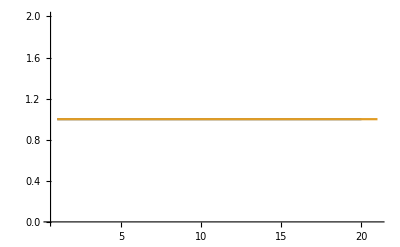

```mathematica
Pn=Module[
{t1,t2},
t1=Quiet@Table[
TSol[2.0,1.0,ϕ,10.0,0.0 Degree,0.5],
{ϕ,0,π/2,π/(2 20)}
];
t2=Table[
1,
{ϕ,Length[t1]}
];
ListPlot[{t1,t2},
Joined->True,
PlotRange->All
]
]
```

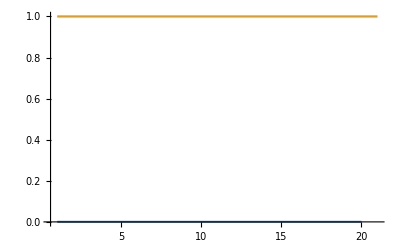

```mathematica
Pn=Module[
{t1,t2},
t1=Quiet@Table[
RSol[2.0,1.0,ϕ,10.0,0.0 Degree,0.5],
{ϕ,0,π/2,π/(2 20)}
];
t2=Table[
1,
{ϕ,Length[t1]}
];
ListPlot[{t1,t2},
Joined->True,
PlotRange->All
]
]
```

```mathematica
Quiet@PolarPlot[
{
TSol[2.0,1.0,ϕ,10.0,0.0 Degree,1.0]
},
{ϕ,-π/2,π/2},
PlotStyle->{Black,Red, Blue},
PolarAxes->True,
MaxRecursion->5,
PolarGridLines->Automatic,
PlotRange->{{-0.1,1},{-0.9,0.9}},
PolarAxesOrigin->{0,1},
ImageSize->{400,400}
]
```

-Graphics-

```mathematica
√(2 9.8 6)
```

10.8444

```mathematica
TSolP[V0_,E0_,ϕV1p_,Wb_,α_,γ0_]:=Module[
{
Iϕs1,Iϕs1r,
Iϕs2,Iϕs2r,
Ik2xp,Ik2xpR,
Ik1xp,
s
},
Iϕs1=ϕV1p;
Iϕs1r=π-ϕV1p;
Iϕs2=ArcSin[(E0/Abs[E0-V0])Sin[ϕV1p]];
Iϕs2r=π-Iϕs2;
Ik1xp=E0 Cos[ϕV1p];
Ik2xp=Abs[V0-E0] Cos[Iϕs2];
Ik2xpR=-Ik2xp;
(**)
s=Sign[E0]Sign[E0-V0];
(Abs@t[Iϕs1,Iϕs1r,Iϕs2,Iϕs2r,Ik2xp,Ik2xpR,Ik1xp,Wb,s])^2
]
```

```mathematica
TSol[8.0,4.0,45 Degree,2.0,0.0,1.0]
```

1.

```mathematica
TSolP[8.0,4.0,45 Degree,2.0,0.0,1.0]
```

1.

```mathematica
Sin[%]
```

0.841471

```mathematica
Sin[1./(2 √2)]
```

0.346234

```mathematica
TSol[8.0,4.0,45Degree,2.0,0.0,1.0]
```

1.

```mathematica
Quiet@PolarPlot[
{
TSolP[2.0,1.0,ϕ,2.0,0.0 Degree,1.0]
},
{ϕ,-π/2,π/2},
PlotStyle->{Black,Red, Blue},
PolarAxes->True,
MaxRecursion->5,
PolarGridLines->Automatic,
PlotRange->{{-0.1,1},{-0.9,0.9}},
PolarAxesOrigin->{0,1},
ImageSize->{400,400}
]
```

-Graphics-

```mathematica
TSol[2.0,1.0,π/6,7.0,10 Degree,0.5]
```

1.04359

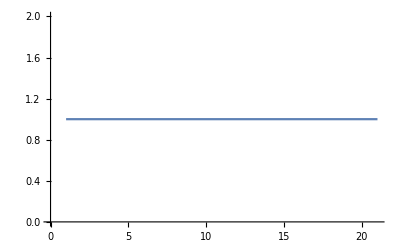

```mathematica
FuT=Table[
TSol[2.0,1.0,ϕ,7.0,0.0 Degree,0.5],
{ϕ,0,π/4,π/(4 20)}
];
ListPlot[FuT,Joined->True]
```

```mathematica
Quiet@PolarPlot[
{
TSol[5.0,1.0,ϕ,50.0,0 Degree,0.5],
RSol[5.0,1.0,ϕ,50.0,0 Degree,0.5],
TSol[5.0,1.0,ϕ,50.0,0 Degree,0.5]+RSol[5.0,1.0,ϕ,50.0,0 Degree,0.5]
},
{ϕ,-π/2,π/2},
PlotStyle->{Black,Red,Blue},
PolarAxes->True,
MaxRecursion->5,
PolarGridLines->Automatic,
PlotRange->{{-0.1,1},{-0.9,0.9}},
PolarAxesOrigin->{0,1},
ImageSize->{400,400}
]
```

-Graphics-

```mathematica
(10+10+10+9.6+10+9.7+10)/8
```

8.6625

```mathematica
Mean[{700,97,}]
```

(797+Null)/3

```mathematica
Length[]
```

Length::argx: Length called with 0 arguments; 1 argument is expected.

Length[]

```mathematica
Quiet@PolarPlot[
{
TSol[5.0,1.0,ϕ,50.0,30 Degree,0.5],
RSol[5.0,1.0,ϕ,50.0,30 Degree,0.5],
TSol[5.0,1.0,ϕ,50.0,30 Degree,0.5]+RSol[5.0,1.0,ϕ,50.0,30 Degree,0.5]
},
{ϕ,-π/2,π/2},
PlotStyle->{Black,Red,Blue},
PolarAxes->True,
MaxRecursion->5,
PolarGridLines->Automatic,
PlotRange->{{-0.1,1.5},{-2.0,2.0}},
PolarAxesOrigin->{0,1},
ImageSize->{400,400}
]
```

-Graphics-

```mathematica
Quiet@PolarPlot[
{
RSol[2.0,1.0,ϕ,7.0,40 Degree,0.5]
},
{ϕ,-π/2,π/2},
PlotStyle->Thick,
PolarAxes->True,
MaxRecursion->5,
PolarGridLines->Automatic,
PlotRange->{{-0.1,1},{-0.9,0.9}},
PolarAxesOrigin->{0,1},
ImageSize->{400,400}
]
```

-Graphics-

```mathematica
Pause[1000]
```

$Aborted

## Calculation of the transmission - graphene

```mathematica
Eq1:=1+r==a+b
```

```mathematica
Eq2:=Exp[ⅈ ϕs1]+r Exp[ⅈ ϕs1r]==s(a Exp[ⅈ ϕs2]+b Exp[ⅈ ϕs2r])
```

```mathematica
Eq3:=a Exp[ⅈ k2xp Wb]+b Exp[ⅈ k2xpR Wb]==t Exp[ⅈ k1xp Wb]
```

```mathematica
Eq4:=a Exp[ⅈ k2xp Wb]Exp[ⅈ ϕs2]+b Exp[ⅈ k2xpR Wb]Exp[ⅈ ϕs2r]==t s Exp[ⅈ k1xp Wb]Exp[ⅈ ϕs1]
```

```mathematica
tSol=Simplify[(t/.Solve[
{Eq1,Eq2,Eq3,Eq4},
{r,a,b,t}
]/.s^2->1)[[1]]
]
```

-((ⅇ^(-ⅈ (k1xp-k2xp-k2xpR) Wb) (ⅇ^(ⅈ ϕs1)-ⅇ^(ⅈ ϕs1r)) (ⅇ^(ⅈ ϕs2)-ⅇ^(ⅈ ϕs2r)))/(-ⅇ^(ⅈ (k2xpR Wb+ϕs1+ϕs2))+ⅇ^(ⅈ (k2xp Wb+ϕs1r+ϕs2))+ⅇ^(ⅈ (k2xp Wb+ϕs1+ϕs2r))-ⅇ^(ⅈ (k2xpR Wb+ϕs1r+ϕs2r))-ⅇ^(ⅈ (k2xp Wb+ϕs1+ϕs1r)) s+ⅇ^(ⅈ (k2xpR Wb+ϕs1+ϕs1r)) s-ⅇ^(ⅈ (k2xp Wb+ϕs2+ϕs2r)) s+ⅇ^(ⅈ (k2xpR Wb+ϕs2+ϕs2r)) s))

```mathematica
A[ϕs1_,ϕs1r_,ϕs2_,ϕs2r_,k2xp_,k2xpR_,k1xp_,Wb_]:=-ⅇ^(-ⅈ (k1xp-k2xp-k2xpR) Wb) (ⅇ^(ⅈ ϕs1)-ⅇ^(ⅈ ϕs1r)) (ⅇ^(ⅈ ϕs2)-ⅇ^(ⅈ ϕs2r))
```

```mathematica
B[ϕs1_,ϕs1r_,ϕs2_,ϕs2r_,k2xp_,k2xpR_,k1xp_,Wb_,s_]:=-ⅇ^(ⅈ (k2xpR Wb+ϕs1+ϕs2))+ⅇ^(ⅈ (k2xp Wb+ϕs1r+ϕs2))+ⅇ^(ⅈ (k2xp Wb+ϕs1+ϕs2r))-ⅇ^(ⅈ (k2xpR Wb+ϕs1r+ϕs2r))-ⅇ^(ⅈ (k2xp Wb+ϕs1+ϕs1r)) s+ⅇ^(ⅈ (k2xpR Wb+ϕs1+ϕs1r)) s-ⅇ^(ⅈ (k2xp Wb+ϕs2+ϕs2r)) s+ⅇ^(ⅈ (k2xpR Wb+ϕs2+ϕs2r)) s
```

```mathematica
t[ϕs1_,ϕs1r_,ϕs2_,ϕs2r_,k2xp_,k2xpR_,k1xp_,Wb_,s_]:=A[ϕs1,ϕs1r,ϕs2,ϕs2r,k2xp,k2xpR,k1xp,Wb]/B[ϕs1,ϕs1r,ϕs2,ϕs2r,k2xp,k2xpR,k1xp,Wb,s]
```

```mathematica
TSol[V0_,E0_,ϕV1p_,Wb_,α_,γ0_]:=Module[
{
Iϕs1,Iϕs1r,
Iϕs2,Iϕs2r,
Ik2xp,Ik2xpR,
Ik1xp,
s
},
Iϕs1=Oϕs[ϕV1p,α,γ0,E0];
Iϕs1r=Oϕsr[ϕV1p,α,γ0,E0];
Iϕs2=Oϕs2[ϕV1p,α,γ0,E0,V0];
Ik1xp=k1xp[ϕV1p,α,γ0,E0];
Iϕs2r=Oϕsr2[ϕV1p,α,γ0,E0,V0];
Ik2xp=k2xp[ϕV1p,α,γ0,E0,V0];
Ik2xpR=k2xpR[ϕV1p,α,γ0,E0,V0];
(**)
s=Sign[E0]Sign[E0-V0];
(Abs@t[Iϕs1,Iϕs1r,Iϕs2,Iϕs2r,Ik2xp,Ik2xpR,Ik1xp,Wb,s])^2
]
```

```mathematica
(*TSol[V0_,E0_,ϕV1p_,Wb_,α_,γ0_]*)
```

```mathematica
TSol[2.0,1.0,π/8,7.0,-(π/8),1.0]
```

0.973798

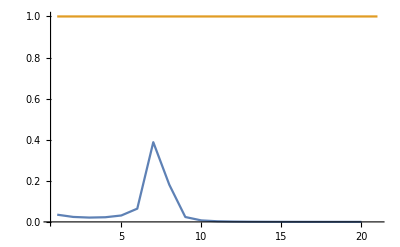

```mathematica
Pn=Module[
{t1,t2},
t1=Quiet@Table[
TSol[2.0,1.0,ϕ,7.0,40 Degree,0.3],
{ϕ,0,π/2,π/(2 20)}
];
t2=Table[
1,
{ϕ,Length[t1]}
];
ListPlot[{t1,t2},
Joined->True,
PlotRange->All
]
]
```

```mathematica
Quiet@PolarPlot[
{
TSol[2.0,1.0,ϕ,3.0,45.0 Degree,1.0],
TSol[2.0,1.0,ϕ,5.0,45.0 Degree,1.0],
TSol[2.0,1.0,ϕ,7.0,45.0Degree,1.0]
},
{ϕ,-π/2,π/2},
PlotStyle->{Black,Red,Darker@Green},
PolarAxes->True,
MaxRecursion->5,
PolarGridLines->Automatic,
PlotRange->{{-0.1,1},{-0.9,0.9}},
PolarAxesOrigin->{0,1},
ImageSize->{400,400}
]
```

$Aborted